Valor resultante: “yield” (total de força acumulada ou gerada).
Deveria ser ao longo do tempo, pela curva... poderia ser infinito ou não. Poderia ser um índice, tipo 1 é estável, 0 é fim instantâneo, >1 é perpetuação.
Uma curva, podendo haver perpetuação (>1) por um certo período de tempo, depois diminuição, até chegar a zero com uma curva determinada.
Aí talvez para explicar uma curva gerada.

Modelar evoluções não constantes com mais de um efeito no modelo, com um elemento estando em um efeito a qualquer momento, e os efeitos interagindo entre si.
Porém modelar apenas uma troca de um efeito por outro dadas certas condições, ou uma condição simples como um intervalo de tempo (talvez calculado com base nas variáveis).
A passagem do tempo faria os elementos já “encontrados” mudarem de comportamento determinando uma mudança na curva observada.

#### Variáveis:

Força inicial

Direção (possibilidade de encontro)

Transmissibilidade do efeito em geral, havendo encontro

Receptividade do efeito em geral, havendo encontro

Transmissibilidade do efeito pelo elemento transmissor (variável randômica)

Receptividade do efeito pelo elemento receptor (variável randômica)

Perda de força básica

## Modelo simples

Força inicial com perda por distância. A cada tantos x, perde força em tantos. Se perder força suficiente, morre, se não, fica estável, ou cresce exponencialmente.
Um elemento ativa os próximos dois e assim por diante. (Esse número poderia ser uma variável mas pode ser fixo de acordo com a reação da fissão.)

Obter parâmetros para a morte, estabilização, e crescimento exponencial.

## Modelo 3

Ponto estacionário: pontos de tangente paralela ao eixo x (horizontal).

Na minha “reação”, a função não poderia crescer, depois decrescer, etc.. Poderia haver no máximo 1 ponto de inflexão “no meio”...
Haveria um ponto de inflexão “inicial” “obrigatório”, do crescimento inicial, que é suposto. Chamando o eixo y de E, a função tem um máximo > 0.
Este ponto de inflexão inicial poderia ser o único, no caso de uma função que cresce exponencialmente e continuamente. Não. Em algum ponto, tem de haver um retorno ao 0. Ou não? Uma reação em cadeia poderia ser potencialmente infinita. Em que ponto a função exponencial adquire um segundo ponto de inflexão?

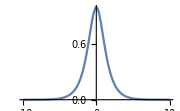
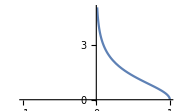

```mathematica
{
Plot[Sech[x],{x,-10,10},ImageSize->Small],
Plot[ArcSech[x],{x,-1,1},ImageSize->Small]
}
```

Função da distribuição normal?

```mathematica
DynamicModule[{a=2.5,n=1},Plot[a ArcTanh[x^n],{x,-1,1},ImageSize->Small]]
```

```mathematica
DynamicModule[{a=2.5,n=3},Plot[a ArcTanh[x^n],{x,-1,1},ImageSize->Small]]
```

Generalized bell function1:

```mathematica
Manipulate[
c=0;
Plot[1/(1+Abs[(x-c)/a]^(2b)),{x,-100,100},ImageSize->Medium,PlotRange->{{-10,10},{0,1.1}}],
{{a,1},0.1,20,.1,Appearance->"Labeled"},
{{b,1},0.1,10,.1,Appearance->"Labeled"}
]
```

Com a>0,b>0;
c no ponto em que f(0)=0;

-a é simétrico em torno de 0.
-Há um “teto” em x=c (?). É um limite para y no centro da função. Este limite pode ser dito o máximo de retorno sustentado da reação.
-A curva tem sempre limite 0 em -∞ e +∞.
-Há um ponto em que o “pico”/”teto” se transforma de uma curva em uma “ponta”. E a “ponta” provavelmente é uma curva acentuada, aproximada.

Como “trasladar” a curva para início em f(0)=0?
Pegar exemplo com b alto.
Encontrar x<0 em que y=0. Este deve ser c:
Se 1/(1+Abs[(x-c)/a]^(2b))=0, isolar x.
f(x) nunca é =0. Portanto é impossível “encontrar o início”.

Outro fator: a função deveria não precisar ser simétrica, podendo ter decrescimento diferente do crescimento.

Asymmetric bell-shaped frequency curve:2

```mathematica
Manipulate[
k=1;
Plot[k x^E E^(-1/2 a^2 (x-b)^2),{x,-100,100},ImageSize->Medium,PlotRange->{{0,20},{0,300}}],
{{a,0.39},.01,1,.01,Appearance->"Labeled"},
{{b,6.7},0.1,10,.1,Appearance->"Labeled"}
]
```

General::munfl: Exp[-865.755] is too small to represent as a normalized machine number; precision may be lost.

Começa de y=0, porém falta o “teto”. Colocar o teto.
-Os dois parâmetros são equivalentes em funcionalidade;
-Cada um deles altera o valor E a posição do ponto máximo;
-Funcionam em sentido contrário.

https://math.stackexchange.com/questions/189223/asymmetric-normal-probability-distribution

Sigmóides3:

```mathematica
Clear[sig]
sig=Function[{x,a,c},1/(1+E^(-a (x-c)))];
```

```mathematica
Manipulate[
Plot[sig[x,a,c],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,10},{0,1}}],
{{a,1},.1,2,.1,Appearance->"Labeled"},
{{c,-.2},-10,10,.1,Appearance->"Labeled"}
]
```

Subtrativa.

```mathematica
Manipulate[
Plot[sig[x,a,b]-sig[x,c,d],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,10},{0,1}}],
{{a,1},.1,2,.1,Appearance->"Labeled"},
{{b,-3.9},-10,10,.1,Appearance->"Labeled"},
{{c,1.8},.1,2,.1,Appearance->"Labeled"},
{{d,5.9},-10,10,.1,Appearance->"Labeled"}
]
```

```mathematica
DynamicModule[{a=1.,b=1.8},Plot[sig[x,a,b],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,10},{0,1}},PlotLabel->Style["1/1+ⅇ^(-1 (x - 1.8))",FontSize->18],PlotTheme->"Scientific",ImageSize->Small]]
```

```mathematica
DynamicModule[{a=-1.,b=1.8},Plot[sig[x,a,b],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,10},{0,1}},PlotLabel->Style["1/1+ⅇ^(1 (x - 1.8))",FontSize->18],PlotTheme->"Scientific",ImageSize->Small]]
```

```mathematica
DynamicModule[{a1=1.,a2=1.8,c1=-3.9,c2=5.9},Plot[sig[x,a1,c1]-sig[x,a2,c2],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,10},{0,1}},PlotLabel->Style["1/(1 + SuperscriptBox[ⅇ, -1 (x - 1.8)])-",FontSize->18],PlotTheme->"Scientific"]]
```

```mathematica
DynamicModule[{a1=0.30000000000000004,a2=1.8,c1=-3.9,c2=5.9},Plot[sig[x,a1,c1]-sig[x,a2,c2],{x,-100,100},ImageSize->Medium,PlotRange->{{-20,10},{0,1}},PlotLabel->Style["a=0.3, b=1.8, c=-3.9, d=5.9",FontSize->18],PlotTheme->"Scientific"]]
```

```mathematica
DynamicModule[{a=1,b=-3.9,c=0.4,d=5.9},Plot[sig[x,a,b]-sig[x,c,d],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,20},{0,1}},PlotLabel->Style["a=1, b=-3.9, c=0.4, d=5.9",FontSize->18],PlotTheme->"Scientific"]]
```

```mathematica
DynamicModule[{a=1,b=-3.9,c=1.8,d=-3.8},Plot[sig[x,a,b]-sig[x,c,d],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,15},{0,1}},PlotLabel->Style["d=-3.8",FontSize->18],PlotTheme->"Scientific"]]
```

```mathematica
DynamicModule[{a=1,b=-3.9,c=1.8,d=-1.5999999999999996},Plot[sig[x,a,b]-sig[x,c,d],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,15},{0,1}},PlotLabel->Style["d=-1.6",FontSize->18],PlotTheme->"Scientific"]]
```

```mathematica
DynamicModule[{a=1,b=-3.9,c=1.8,d=3.200000000000001},Plot[sig[x,a,b]-sig[x,c,d],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,20},{0,1.1}},PlotLabel->Style["d=3.2",FontSize->18],PlotTheme->"Scientific"]]
```

```mathematica
DynamicModule[{a=1,b=-3.9,c=1.8,d=14.},Plot[sig[x,a,b]-sig[x,c,d],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,20},{0,1.1}},PlotLabel->Style["d=10",FontSize->18],PlotTheme->"Scientific"]]
```

1	http://researchhubs.com/post/maths/fundamentals/bell-shaped-function.html

2	https://projecteuclid.org/download/pdf_1/euclid.aoms/1177729393

3	http://researchhubs.com/post/engineering/fuzzy-system/fuzzy-membership-function.html

```mathematica
DynamicModule[{a=1,b=-3.9,c=1.8,d=3.200000000000001},Plot[sig[x,a,b]-sig[x,c,d],{x,-100,100},ImageSize->Medium,PlotRange->{{-10,20},{0,1.1}},PlotLabel->Style["d=3.2",FontSize->18],PlotTheme->"Scientific"]]
```